# Exam 1: Carter Colton

```mathematica
Clear["`*" ]
```

## Problem 1

Find the numerical value of √((π/(1 + ln(3)))-(2/(6+e^4))) , to 12 decimal places.

```mathematica
N[Sqrt[(Pi/(1+Log[3]))-(2/(6+E^4))],13]
```

1.209951000804

To make sure that the equation is correct

```mathematica
Sqrt[(Pi/(1+Log[3]))-(2/(6+E^4))]
```

√(-2/(6+ⅇ^4)+π/(1+Log[3]))

## Problem 2

Create a list of what the function f(x) = J_0(x)/x^4 is equal to, for x = 1, 2, 3, 4 and 5  (in numerical form) (Here, J_0 refers to the “zeroth-order Bessel function of the first kind” (see BesselJ)).

```mathematica
N[Table[((BesselJ[0,x])/x^4),{x,1,5}]]
```

{0.765198,0.0139932,-0.00321052,-0.00155137,-0.000284155}

## Problem 3

Put this algebraic expression in simplest form:  1/(3(1+x)) - (-1 + 2x)/(6(1-x+x^2)) + 2/(3(1 + 1/3(-1 + 2x)^2)).  (Don’t worry about x possibly equaling something that causes the denominators to be zero.)

```mathematica
Simplify[ 1/(3(1+x))-(-1 + 2x)/(6(1-x+x^2))+2/(3(1 + 1/3(-1 + 2x)^2))]
```

1/(1+x^3)

## Problem 4

With each step George goes 1/4 the distance from himself to a wall (one “unit” away). With his first step he goes 1/4 units, with his second step he goes 1/4 of the remaining 3/4 units = 3/16 units, with his third step he goes 1/4 of (1 – 1/4 – 3/16) units = 9/64 units, etc. The pattern is such that the next few steps are 27/256 units, 81/1024 units, 3^5/4^6 units, 3^6/4^7 units, etc. After an infinite number of steps, how far has he gone? (And does he reach the wall?)

```mathematica
1/4+Sum[3^(x)/4^(x+1),{x,1,Infinity}]
```

1

After an infinite number of steps, the series converges to one, so after all those steps, he has basically gone the entire way to the wall. Therefore, if he were to actually take an infinite number of steps, he would reach the wall.

## Problem 5

Find what x equals, at the intersection(s) of y = ⅇ^x-5 and y = ln x.  Then calculate the sine of that (those) value(s). (If there is more than one solution, find each solution and calculate the sine at each value.)  As a reminder, your code must automatically generate the final answer, so you cannot use any copying & pasting or typing in of the answer to the first part. Instead, use a “slash dot” command to gain access to the value obtained by the first part.

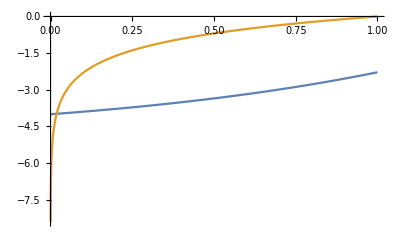

```mathematica
Plot[{E^x-5,Log[x]},{x,0,1}]
```

```mathematica
FindRoot[E^x-5==Log[x],{x,.025}]
```

{x→0.018664}

```mathematica
x/.%
```

0.018664

```mathematica
Sin[x]/.x->%
```

0.0186629

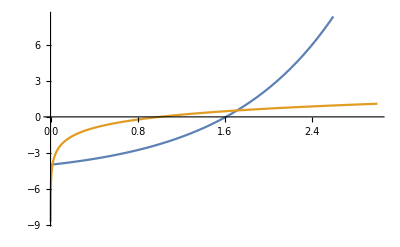

```mathematica
Plot[{E^x-5,Log[x]},{x,0,3}]
```

```mathematica
FindRoot[E^x-5==Log[x],{x,1.7}]
```

{x→1.71152}

```mathematica
x/.%
```

1.71152

```mathematica
Sin[x]/.x->%
```

0.990114

## Problem 6

Suppose you have a sphere of radius R, whose mass density ρ varies with distance from the center according to this formula: ρ = C (1-r/R)  (e^(-r/R))_.  (C is a constant that has units of kg/m^3 and r is the distance from the center of the sphere.) In other words, the mass is more concentrated at the center of the sphere than it is towards the edge. How much total mass is inside the sphere? To find this you must compute the integral ∫∫∫   ρ   dx dy dz, with dx dy dz converted into spherical coordinates as done in one of the assignments in the Integration lab. Be sure to use the proper limits of integration as also explained in that assignment.

```mathematica
integrand=R^2*Sin[theta]*c*(1-r/R)*E^(-r/R);
```

```mathematica
Integrate[integrand,{phi,0,2*Pi},{theta,0,Pi}, Assumptions->{R>0,r>0, r ≠ R}]
```

-4 c ⅇ^(-r/R) π (r-R) R

## Problem 7

Plot the field lines (StreamPlot) and equipotential contours (ContourPlot) for the following set of charges which mimic a parallel plate capacitor:  eleven positive charges at locations (-5, 2), (-4, 2), ..., (+5, 2);  and eleven negative charges at locations (-5, -2), (-4, -2), ..., (+5, -2). Use the same technique as used in the differentiation lab. All charges have magnitude 1, and as done in that lab, set all multiplicative constants equal to 1. Make your plots with x and y both going from -10 to 10, and superimpose the two plots. The two sets of lines should be perpendicular to each other, and your results should look somewhat like what you learned about the field & equipotential lines of a capacitor in Physics 220. Hint: I advise you to add up the charges in some clever way rather than manually typing out the combined electric potential from all 22 charges.

```mathematica
Vbase = q/Sqrt[x^2+y^2];
V = Sum[Vbase /. {q->1,x-> x-Table[x,{x,-5,5,1}], y-> y-(-2)},{n,1}]
Vpositive = Sum[Vbase /. {q-> 1,x-> x-Range[-5,5,1], y-> y-(2)}, {n,1}]
```

{1/(√((5+x)^2+(2+y)^2)),1/(√((4+x)^2+(2+y)^2)),1/(√((3+x)^2+(2+y)^2)),1/(√((2+x)^2+(2+y)^2)),1/(√((1+x)^2+(2+y)^2)),1/(√(x^2+(2+y)^2)),1/(√((-1+x)^2+(2+y)^2)),1/(√((-2+x)^2+(2+y)^2)),1/(√((-3+x)^2+(2+y)^2)),1/(√((-4+x)^2+(2+y)^2)),1/(√((-5+x)^2+(2+y)^2))}

{1/(√((5+x)^2+(-2+y)^2)),1/(√((4+x)^2+(-2+y)^2)),1/(√((3+x)^2+(-2+y)^2)),1/(√((2+x)^2+(-2+y)^2)),1/(√((1+x)^2+(-2+y)^2)),1/(√(x^2+(-2+y)^2)),1/(√((-1+x)^2+(-2+y)^2)),1/(√((-2+x)^2+(-2+y)^2)),1/(√((-3+x)^2+(-2+y)^2)),1/(√((-4+x)^2+(-2+y)^2)),1/(√((-5+x)^2+(-2+y)^2))}

```mathematica
Vx=-D[V,x];
Vxpositive=-D[Vpositive,x];
```

```mathematica
Vy=-D[V,y];
Vypositive=-D[Vpositive,y];
```

```mathematica
Show[StreamPlot[{Vx,Vxpositive,Vy,Vypositive},{x,-10,10},{y,-10,10}],ContourPlot[{V,Vpositive},{x,-10,10},{y,-10,10},ContourShading->None,ColorFunction->"Rainbow"]]
```

-Graphics-

```mathematica
Show[StreamPlot[{Vx,Vy},{x,-10,10},{y,-10,10}],ContourPlot[{V},{x,-10,10},{y,-10,10},ContourShading->None,ColorFunction->"Rainbow"]]
```

-Graphics-

```mathematica
Vtest = Sum[Vbase /. {q-> RandomReal[{-1,1}],x-> x-RandomReal[{-1,1}], y-> y-RandomReal[{-1,1}]}, {n,1,10}];
```

```mathematica
Vxtest=-D[Vtest,x];
Vytest=-D[Vtest,y];
```

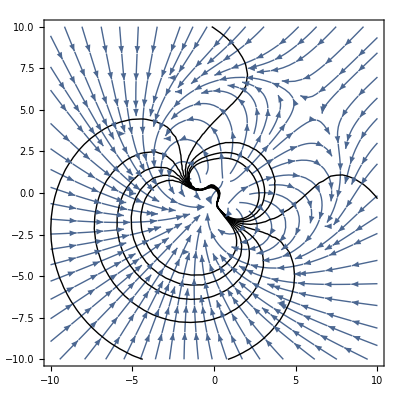

```mathematica
Show[StreamPlot[{Vxtest,Vytest},{x,-10,10},{y,-10,10}],ContourPlot[{Vtest},{x,-10,10},{y,-10,10},ContourShading->None,ColorFunction->"Rainbow"]]
```

## Problem 8

Create a graphics object of a smiley-face by combining several elements (Circle, Disk, etc.) together.  Your face should include two eyes, a mouth, and a nose and use at least two different colors.   Hint: A smile can be created using an elliptical arc.  An elliptical arc can be done with the Circle command; read about it and play around with the options for the angles θ_1 and θ_2 until it looks like a smile.

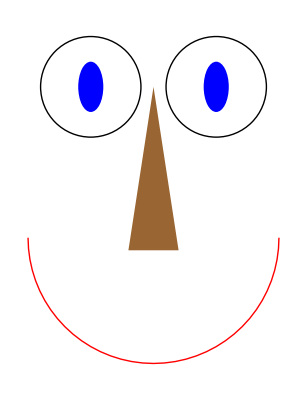

```mathematica
Graphics[{Black,Circle[{-1,4},{4,4}],Blue,Disk[{-1,4},{1,2}],Black,Circle[{9,4},{4,4}],Blue,Disk[{9,4},{1,2}],Brown,Triangle[{{2,-9},{4,4},{6,-9}}],Red,Circle[{4,-8},10,{0,-Pi}],Axes->True}]
```

## Problem 9

The integration lab discussed orthogonal functions, which are functions whose product integrates to zero over a particular range. One example was sine functions: sin(nx) and sin(mx) are orthogonal over the range from 0 to 2π  when n≠m.  Another example, given in the extra credit problem, was the Legendre polynomials: L_n(x) and L_m(x) are orthogonal over the range from -1 to 1 when n≠m.

Another class of orthogonal functions are the “Hermite polynomials”, H_n(x), given in Mathematica by the function HermiteH[n,x]. They are a set of polynomials which arise in quantum mechanics when solving for the wave functions of a spring-like potential (commonly called the “quantum harmonic oscillator” problem). The Hermite polynomials are orthogonal over the range from -∞ to +∞, but an additional “weighting function” of e^(-x^2)must be included in the integral. That is, ∫_(-∞)^∞ H_n(x)H_m(x)e^(-x^2)dx  = 0  if n≠m.

(a) Generate a list of the first six Hermite polynomials (i.e. m runs from 0 to 5) and plot them all on the same graph over the range {x, -2, 2} (with an appropriate PlotRange selected so you can see them all).
(b) Pick two of the polynomials (different ones), and plot  H_n(x)H_m(x)e^(-x^2) with the Filling→Axis option, to convince yourself it’s plausible that the total area above the graph equals the total area below the graph. Then do the integral with those two specific polynomials (from -∞ to ∞) to show that it does actually equal zero.
(c) Repeat part (b), using two of the same polynomial instead of two different ones. In this case, the graph area will not cancel out and the numerical integral won’t equal zero. 
(d) Now construct a table of values of the integral for all values of m and n. Do this with the Table command, using {n,0,5} and {m,0,5} as options, and display it with TableForm.   (Interesting mathematical sidenote: the integer coefficients multiplying the square root of π along the diagonals of your table are the “double factorials” of the even integers.)

```mathematica
Table[HermiteH[n,x],{n,0,5}]
```

{1,2 x,-2+4 x^2,-12 x+8 x^3,12-48 x^2+16 x^4,120 x-160 x^3+32 x^5}

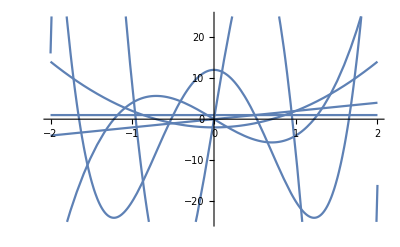

```mathematica
Plot[Table[HermiteH[n,x],{n,0,5}], {x,-2,2},PlotRange->{{-2,2},{-25,25}}]
```

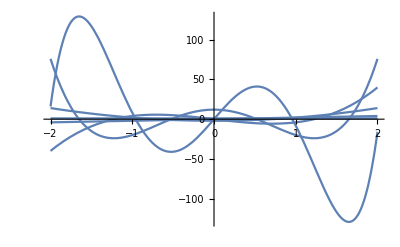

```mathematica
Plot[Table[HermiteH[n,x],{n,0,5}], {x,-2,2},PlotRange->All]
```

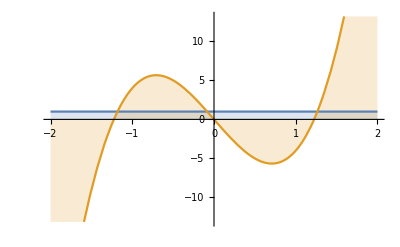

```mathematica
Plot[{HermiteH[0,x],HermiteH[3,x]}, {x,-2,2},Filling->Axis]
```

```mathematica
Integrate[HermiteH[0,x]*HermiteH[3,x]*E^(-x^2), {x,-Infinity,Infinity}]
```

0

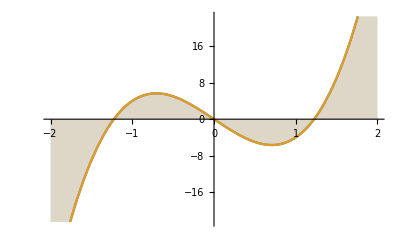

```mathematica
Plot[{HermiteH[3,x],HermiteH[3,x]}, {x,-2,2},Filling->Axis]
```

```mathematica
Integrate[HermiteH[3,x]*HermiteH[3,x]*E^(-x^2), {x,-Infinity,Infinity}]
```

48 √π

```mathematica
Table[Integrate[HermiteH[n,x]*HermiteH[m,x]*E^(-x^2), {x,-Infinity,Infinity}],{n,0,5},{m,0,5}]
```

{{√π,0,0,0,0,0},{0,2 √π,0,0,0,0},{0,0,8 √π,0,0,0},{0,0,0,48 √π,0,0},{0,0,0,0,384 √π,0},{0,0,0,0,0,3840 √π}}

```mathematica
TableForm[%]
```

√π | 0 | 0 | 0 | 0 | 0
0 | 2 √π | 0 | 0 | 0 | 0
0 | 0 | 8 √π | 0 | 0 | 0
0 | 0 | 0 | 48 √π | 0 | 0
0 | 0 | 0 | 0 | 384 √π | 0
0 | 0 | 0 | 0 | 0 | 3840 √π

## Problem 10

(a) Make a 3D plot of the function f5(x,y) = sinc^2(x)  sinc^2(2y) with the x and y axes both going from -9 to 9. This is the diffraction pattern you’d get by shining coherent light through a rectangular slit. Use PlotRange->All in order to see all of the main peak.
(b) Make a second plot of the function, this time choosing a plot range from 0 to 0.05 so that you can see some of the finer details (smaller peaks). Use enough PlotPoints so that there’s no distortion of the peaks.

```mathematica
f5[x_,y_]=(Sinc[x])^2*(Sinc[2*y])^2
```

Sinc[x]^2 Sinc[2 y]^2

```mathematica
Plot3D[f5[x,y],{x,-9,9},{y,-9,9},PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[f5[x,y],{x,-9,9},{y,-9,9},PlotRange->All,PlotPoints->50]
```

-Graphics3D-

```mathematica
Plot3D[f5[x,y],{x,-9,9},{y,-9,9},PlotRange->{0,0.05},PlotPoints->100]
```

-Graphics3D-